# Intermittent Feeding Model

## Two Species Case

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=.75,(*Clearance rate 1*)
c2=.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10^(-2)k,(*Initial Condition*)
tfim=220,(*Final time*)
frac1=0.2(*Fraction in the food of species 1*)
};

t0=0;(*Initial time*)

cor1=RGBColor["#D81B60"]; (*Good color 1 for pictures*)
cor2=RGBColor["#1E88E5"];(*Good color 2 for pictures*)
```

### Situation 0 - No feeding

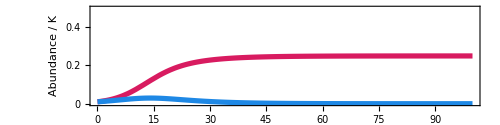

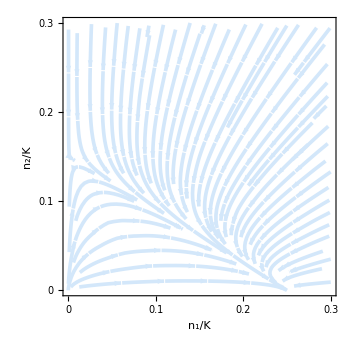

```mathematica
(*----------------Solution----------------*)

arrows={};(*used to construct the phase portrait*)
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0
},
{n1,n2},
{t,t0,tfim},
MaxStepSize->0.001,
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

NoFeeding=Show[
Plot[Evaluate[({n1[t],n2[t]}/k/.#)&/@sol],{t,0,100},PlotLegends->Placed[SwatchLegend[{"Species 1","Species 2"}],{0.125,0.7}],LabelStyle->{FontSize->15,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,0.5},
Frame->True,
FrameStyle->Directive[Black,FontSize->15],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}
]

phasePor=StreamPlot[
{r1*x1*k(1-(x1*k+x2*k)/k)-c1*x1*k,r2*x2*k(1-(x1*k+x2*k)/k)-c2*x2*k}
,{x1,0,300/k},{x2,0,300/k},
PlotRange->{{0,300/k},{0,300/k}},
PlotLegends->BarLegend[Automatic,LegendMarkerSize->250],
ImageSize->350,
StreamColorFunction->None,
StreamStyle->Directive[Thickness[0.0075],Lighter@Lighter@Lighter@Lighter@cor2],
StreamScale->Medium,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{"n_1/K","n_2/K","Phase Portrait"},
LabelStyle->Directive[Black,FontSize->15],
FrameTicks->{{{0,0.1,0.2,0.3},None},{{0,0.1,0.2,0.3},None}}
]
```

### Situation 1 - Species 1 more abundant

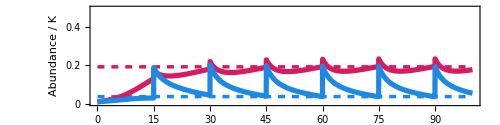

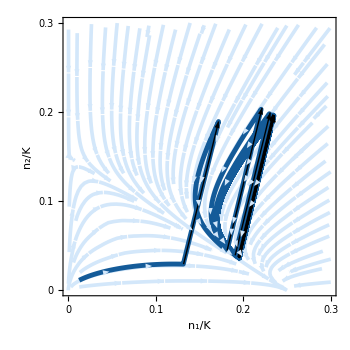

```mathematica
(*----------------Parameters----------------*)

τ0=15; (*Time between meals*)
nf=200;(*Total amount of microbes in each meal*)

(*----------------Solution----------------*)

arrows={};(*used to construct the phase portrait*)
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ0]==0,
{n1[t]->n1[t]+nf(frac1),
n2[t]->n2[t]+nf(1-frac1),
AppendTo[arrows,{{n1[t]-nf*frac1,n2[t]-nf*(1-frac1)},{n1[t],n2[t]}}]
}
]
},
{n1,n2},
{t,t0,tfim},
MaxStepSize->0.001,
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

Solution1=Show[
Plot[{193/k,37.2/k},{t,0,100},PlotStyle->{{cor1,Thickness[0.005],Dashed},{cor2,Thickness[0.005],Dashed}},Axes->False],
Plot[Evaluate[({n1[t],n2[t]}/(k)/.#)&/@sol],{t,0,100},(*PlotLegends->Placed[SwatchLegend[{"n_1","n_2"}],{0.08,0.75}],*)LabelStyle->{FontSize->18,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,0.5},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}]


parPlotRandTimes=Show[
phasePor,
ParametricPlot[Evaluate[({n1[t],n2[t]}/k/.#)&/@sol],{t,1,tfim},
PlotRange->{{0,300/k},{0,300/k}},
PlotStyle->Directive[Darker@cor2,Thickness[0.01]],
ImageSize->350,
Frame->True,
FrameStyle->Directive[Black,FontSize->15],
FrameLabel->{"n_1","n_2","Phase Portrait"},
LabelStyle->Directive[Black,FontSize->15],
AspectRatio->1,PlotPoints->120
(*FrameTicks->None*)
],
Graphics[Drop[Arrow/@(arrows/k),0]],
Axes->False]
```

### Situation 2 - Species 2 more abundant

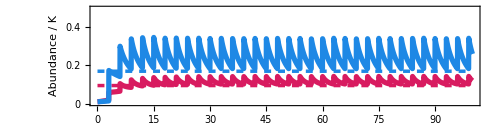

```mathematica
(*----------------Parameters----------------*)

τ0=3; (*Time between meals*)
nf=200;(*Total amount of microbes in each meal*)

(*----------------Solution----------------*)

arrows={};(*used to construct the phase portrait*)
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ0]==0,
{n1[t]->n1[t]+nf(frac1),
n2[t]->n2[t]+nf(1-frac1),
AppendTo[arrows,{{n1[t]-nf*frac1,n2[t]-nf*(1-frac1)},{n1[t],n2[t]}}]
}
]
},
{n1,n2},
{t,t0,tfim},
MaxStepSize->0.001,
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

Solution2=Show[
Plot[{95/k,170/k},{t,0,100},PlotStyle->{{cor1,Thickness[0.005],Dashed},{cor2,Thickness[0.005],Dashed}},Axes->False],
Plot[Evaluate[({n1[t],n2[t]}/(k)/.#)&/@sol],{t,0,100},(*PlotLegends->Placed[SwatchLegend[{"n_1","n_2"}],{0.08,0.75}],*)LabelStyle->{FontSize->18,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,1/2},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}]
```

## Heatmap of

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=0.75,(*Clearance rate 1*)
c2=0.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10,(*Initial Condition*)
tfim=1000,(*Final time*)
frac1=0.2(*Fraction in the food of species 1*)
};

t0=0;(*Initial time*)

cor1=RGBColor["#D81B60"]; (*Good color 1 for pictures*)
cor2=RGBColor["#1E88E5"];(*Good color 2 for pictures*)

τ0=0.1;
nf0=2;
dir=NotebookDirectory[]<>"HeatMap-Data2\\";
```

### Exporting data

```mathematica
τ0=0.1;
nf0=1.;

Export[dir<>"params.txt",Params,"TABLE"]

eqs={n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t]};
{n01,n02}={n0,n0};
ini={n1[0]==n0,n2[0]==n0};
solNoFeed=NDSolve[Join[eqs,ini],{n1,n2},{t,0,tfim}];

SetSharedVariable[resNumericTab];

Do[
resNumericTab={};
nf=nfx;

ParallelDo[
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ]==0,
{n1[t]->n1[t]+nf(frac1),
n2[t]->n2[t]+nf(1-frac1)}]},
{n1,n2},
{t,t0,tfim},
MaxStepSize->0.001,
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}}
];

nCycles=20;

res=Quiet@NIntegrate[Evaluate[(-(n1[t]/(n1[t]+n2[t]))*Log[(n1[t]/(n1[t]+n2[t]))]-(n2[t]/(n1[t]+n2[t]))*Log[(n2[t]/(n1[t]+n2[t]))])/.First[sol]],{t,750,750+nCycles*τ},Method->"Trapezoidal"]/(nCycles*τ);

AppendTo[resNumericTab,{τ,res}]
,{τ,τ0,12,15/100}];

Export[dir<>"DIV-nf-"<>ToString[nf]<>".txt",resNumericTab,"TABLE"]

,{nfx,2,200}]
```

### Importing Data

```mathematica
dir=NotebookDirectory[]<>"HeatMap-Data2\\";

tab=Table[dat=Sort@Import[dir<>"DIV-nf-"<>ToString[nf]<>".txt","TABLE"];
tau=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{tau,Table[nf,{Length[tau]}],Shannon}],
{nf,2,200}];
tab2=Flatten[tab,1];
```

### Image Heatmap

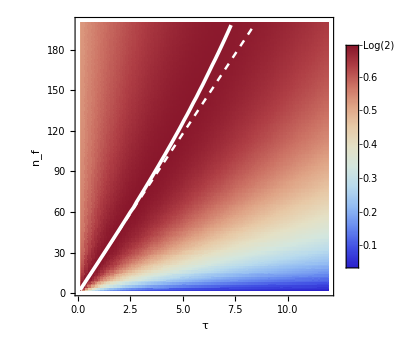

```mathematica
nfPeak=Flatten[Quiet@FindArgMax[#[x],x]&/@(ListInterpolation/@Transpose[tab⟦All,All,3⟧])]+1;(*The +1 is because the listInterpolation gives a function in the range (1->199) instead of (2->200)*)
peaks=Drop[Transpose@{Sort[tau],nfPeak},-31];

heatmap=ListDensityPlot[tab2,InterpolationOrder->0,
PlotLegends->BarLegend[Automatic,Ticks->{0.1,0.2,0.3,0.4,0.5,0.6,{.693,"Log(2)"}},LegendMarkerSize->250],
ColorFunction->ColorData["ThermometerColors"],
ColorFunctionScaling->True,
ImageSize->350,Frame->True,FrameStyle->Directive[Black,FontSize->18],FrameLabel->{"τ","n_f","Shannon Diversity "},
LabelStyle->Directive[Black,FontSize->16]
];

α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);

Show[heatmap,
ListLinePlot[peaks,PlotStyle->{White,PointSize->0.001,Thickness[0.0075]}],
Plot[α τ,{τ,0.1,8.45},PlotStyle->{White,Dashed,Thickness[0.005]}]
]
```

### Solution in first order

#### Analytical

```mathematica
Print[Dynamic@nf]
Print[Dynamic@τ]

Do[
Do[

nL1[NL_]:=frac1*nf*Exp[τ(r1-c1-r1(NL+nf/2)/k)]/(1-Exp[τ(r1-c1-r1(NL+nf/2)/k)]);
nL2[NL_]:=(1-frac1)*nf*Exp[τ(r2-c2-r2(NL+nf/2)/k)]/(1-Exp[τ(r2-c2-r2(NL+nf/2)/k)]);

sol=NSolve[nL1[NL]+nL2[NL]==NL,NL,PositiveReals];

aux={nL1[NL],nL2[NL]}/.sol;
pos=Flatten@Position[aux,{_?Positive,_?Positive}];
sol=sol[[pos]];

nMeanNorm={(nL1[NL]+frac1*nf/2)/(NL+nf/2),(nL2[NL]+(1-frac1)*nf/2)/(NL+nf/2)}/.First[sol];
H[nf,τ]=-Total[nMeanNorm*Log[nMeanNorm]];
,{τ,τ0,12,0.05}]

,{nf,{10,25,50,75,100}}]
```

#### Image

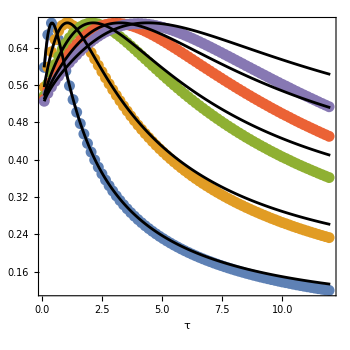

```mathematica
sol1Order=ListLinePlot[Table[{τ,H[nf,τ]},{nf,{10,25,50,75,100}},{τ,τ0,12,0.05}],PlotStyle->Black,ScalingFunctions->{None}];

imageH=ListPlot[Table[tab⟦i-1⟧[[All,{1,3}]],{i,{10,25,50,75,100}}],ColorFunction->Function[{x,y},ColorData["ThermometerColors"][y]],
PlotRange->All,
PlotStyle->Directive[PointSize->0.0225],
Joined->True,
Mesh->Automatic,
ImageSize->350,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{"τ",""},
LabelStyle->Directive[Black,FontSize->15],
AspectRatio->1
];

Show[imageH,
sol1Order,
PlotRange->All
]
```